```mathematica
(*You need first to compile the notebook GSU2P_TheorySG2Coupled.nb*)
```

```mathematica
<<MaTeX`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

# GSU2P Progress : Non-viability in general scenarios

## Santiago García-Serna

## The general model

The action of the model is

where

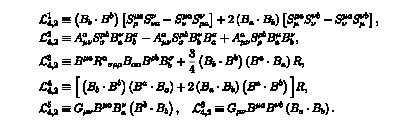

where, under the configuration Β_(0a)(t)=0, B_(i a)(t)=a(t)ψ(t)δ_(i a) and th
e FLRW bakcground the general equations are presented on the next sections.

## General equations without aditional simplifications(No compile without the other notebook)

### General equations on terms of the field

```mathematica
Column@{MaTeX["3m_p^2G_{00}-T_{00}=0",Magnification->1.5],
(2 𝒢[{0,-cb},{0,cb}]/.Ruleda/.Ruleg//Expand)}
```

-Graphics-
-3/2 (ĝ)^2 ψ[t]^4+3 m_P^2 H[t]^2-3/2 ψ[t]^2 H[t]^2+(18 α_3 ψ[t]^4 H[t]^2)/m_P^2+(9 χ_5 ψ[t]^4 H[t]^2)/m_P^2-ρ_m[t]-ρ_r[t]-3 ψ[t] H[t] ψ'[t]-(120 α_1 ψ[t]^3 H[t] ψ'[t])/m_P^2+(156 α_3 ψ[t]^3 H[t] ψ'[t])/m_P^2+(18 χ_5 ψ[t]^3 H[t] ψ'[t])/m_P^2-3/2 ψ'[t]^2+(18 α_3 ψ[t]^2 ψ'[t]^2)/m_P^2+(9 χ_5 ψ[t]^2 ψ'[t]^2)/m_P^2

```mathematica
Column@{MaTeX["3m_p^2G_{11}-T_{11}=0",Magnification->1.5],
(2 𝒢[{1,-cb},{1,cb}]/.Ruleda/.Ruleg//Expand)}
```

-Graphics-
1/2 (ĝ)^2 ψ[t]^4+3 m_P^2 H[t]^2+1/2 ψ[t]^2 H[t]^2+(120 α_1 ψ[t]^4 H[t]^2)/m_P^2-(114 α_3 ψ[t]^4 H[t]^2)/m_P^2+(3 χ_5 ψ[t]^4 H[t]^2)/m_P^2+ρ_r[t]/3+ψ[t] H[t] ψ'[t]+(12 α_3 ψ[t]^3 H[t] ψ'[t])/m_P^2+(6 χ_5 ψ[t]^3 H[t] ψ'[t])/m_P^2+1/2 ψ'[t]^2-(120 α_1 ψ[t]^2 ψ'[t]^2)/m_P^2+(126 α_3 ψ[t]^2 ψ'[t]^2)/m_P^2+(3 χ_5 ψ[t]^2 ψ'[t]^2)/m_P^2+2 m_P^2 H'[t]+(40 α_1 ψ[t]^4 H'[t])/m_P^2-(40 α_3 ψ[t]^4 H'[t])/m_P^2-(40 α_1 ψ[t]^3 ψ''[t])/m_P^2+(40 α_3 ψ[t]^3 ψ''[t])/m_P^2

```mathematica
Column@{MaTeX["\\frac{\\delta S}{\\delta B_{a\\mu}}=0",Magnification->1.5],
(𝒜[{1,-su},{1,-cb}]/.Ruleda/.Ruleg//Expand)}
```

-Graphics-
-2 (ĝ)^2 ψ[t]^3 a[t]-2 ψ[t] a[t] H[t]^2-(120 α_1 ψ[t]^3 a[t] H[t]^2)/m_P^2+(132 α_3 ψ[t]^3 a[t] H[t]^2)/m_P^2+(6 χ_5 ψ[t]^3 a[t] H[t]^2)/m_P^2-3 a[t] H[t] ψ'[t]+(36 α_3 ψ[t]^2 a[t] H[t] ψ'[t])/m_P^2+(18 χ_5 ψ[t]^2 a[t] H[t] ψ'[t])/m_P^2+(12 α_3 ψ[t] a[t] ψ'[t]^2)/m_P^2+(6 χ_5 ψ[t] a[t] ψ'[t]^2)/m_P^2-ψ[t] a[t] H'[t]-(40 α_1 ψ[t]^3 a[t] H'[t])/m_P^2+(52 α_3 ψ[t]^3 a[t] H'[t])/m_P^2+(6 χ_5 ψ[t]^3 a[t] H'[t])/m_P^2-a[t] ψ''[t]+(12 α_3 ψ[t]^2 a[t] ψ''[t])/m_P^2+(6 χ_5 ψ[t]^2 a[t] ψ''[t])/m_P^2

### General equation on dynamical systems

```mathematica
Column@{MaTeX["3m_p^2G_{00}-T_{00}=0",Magnification->1.5],eq1}
```

-Graphics-
-1+𝓎[t]^2+𝓍[t] (𝓍[t]+2 𝓎[t])+(-2 α_1+(7 α_3)/20) (-480 𝓍[t] 𝓎[t]^3-120 𝓎[t]^4)+α_3 (-216 𝓍[t] 𝓎[t]^3-62 𝓎[t]^4)+2 α_3 (-8 𝓍[t]^2 𝓎[t]^2+8 𝓎[t]^4)-8 α_3 (32 𝓍[t] 𝓎[t]^3+12 𝓎[t]^4)+1/3 (-20 α_1+14 α_3) (96 𝓍[t] 𝓎[t]^3+36 𝓎[t]^4)+α_1 (40 𝓎[t]^4+𝓍[t] (40 𝓍[t] 𝓎[t]^2-80 𝓎[t]^3))+χ_6 (-24 𝓎[t]^4+𝓍[t] (-24 𝓍[t] 𝓎[t]^2-48 𝓎[t]^3))+χ_5 (-12 𝓎[t]^4+𝓍[t] (-12 𝓍[t] 𝓎[t]^2-24 𝓎[t]^3))+(5 α_1+α_3-χ_4/2-3 χ_6) (-8 𝓎[t]^4+𝓍[t] (-8 𝓍[t] 𝓎[t]^2-16 𝓎[t]^3))+χ_4 (-4 𝓎[t]^4+𝓍[t] (-4 𝓍[t] 𝓎[t]^2-8 𝓎[t]^3))+2 𝓏[t]^4+Ωm[t]+Ωr[t]

```mathematica
Column@{MaTeX["3m_p^2G_{11}-T_{11}=0",Magnification->1.5],eq2}
```

-Graphics-
3+𝓍[t]^2+2 𝓍[t] 𝓎[t]+𝓎[t]^2+(χ_4+3 χ_5+2 (5 α_1+α_3-χ_4/2-3 χ_6)+6 χ_6) (4 𝓍[t]^2 𝓎[t]^2+8 𝓍[t] 𝓎[t]^3+4 𝓎[t]^4)+2 𝓏[t]^4-2 ϵ[t]+(-20 α_1+6 α_3) (-96 𝓍[t]^2 𝓎[t]^2-16 √2 p[t] 𝓎[t]^3-96 𝓍[t] 𝓎[t]^3+12 𝓎[t]^4-8 𝓎[t]^4 ϵ[t])+2 α_3 (-40 𝓍[t]^2 𝓎[t]^2-8 √2 p[t] 𝓎[t]^3-112 𝓍[t] 𝓎[t]^3-56 𝓎[t]^4+16 𝓎[t]^4 ϵ[t])+α_3 (648 𝓍[t]^2 𝓎[t]^2+108 √2 p[t] 𝓎[t]^3+496 𝓍[t] 𝓎[t]^3-214 𝓎[t]^4+92 𝓎[t]^4 ϵ[t])+α_1 (440 𝓍[t]^2 𝓎[t]^2+80 √2 p[t] 𝓎[t]^3-80 𝓍[t] 𝓎[t]^3-520 𝓎[t]^4+160 𝓎[t]^4 ϵ[t])+(-2 α_1+(7 α_3)/20) (1440 𝓍[t]^2 𝓎[t]^2+240 √2 p[t] 𝓎[t]^3+960 𝓍[t] 𝓎[t]^3-600 𝓎[t]^4+240 𝓎[t]^4 ϵ[t])+Ωr[t]

```mathematica
Column@{MaTeX["\\frac{\\delta S}{\\delta B_{a\\mu}}=0",Magnification->1.5],eq3}
```

-Graphics-
p[t]/(√2)+3 𝓍[t]+2 𝓎[t]+2 α_3 (-8 𝓍[t]^2 𝓎[t]-4 √2 p[t] 𝓎[t]^2-24 𝓍[t] 𝓎[t]^2-16 𝓎[t]^3)+(4 𝓏[t]^4)/𝓎[t]-𝓎[t] ϵ[t]+(-20 α_1+6 α_3) (24 𝓎[t]^3-16 𝓎[t]^3 ϵ[t])+(χ_4+3 χ_5+2 (5 α_1+α_3-χ_4/2-3 χ_6)+6 χ_6) (-4 𝓍[t]^2 𝓎[t]-2 √2 p[t] 𝓎[t]^2-12 𝓍[t] 𝓎[t]^2-4 𝓎[t]^3+4 𝓎[t]^3 ϵ[t])+α_1 (40 𝓍[t]^2 𝓎[t]+20 √2 p[t] 𝓎[t]^2+120 𝓍[t] 𝓎[t]^2-200 𝓎[t]^3+40 𝓎[t]^3 ϵ[t])+α_3 (-200 𝓎[t]^3+108 𝓎[t]^3 ϵ[t])+(-2 α_1+(7 α_3)/20) (-480 𝓎[t]^3+240 𝓎[t]^3 ϵ[t])

## Simplification of the equations and analysis (No compile without the other notebook)

The equation can be simplified using the perturbative criterion for the speed of gravitational waves, the absence of ghosts, and the lack of Laplacian instabilities.

```mathematica
α2:=2α3;
α6:=-20α1+6α3-3α5;
χ3:=0;
α4:=-2α1+7/20 α3;
α5:=-(20α1-14α3)/3;
χ7:=5α1+α3-χ4/2-3χ6;
```

```mathematica
(*convenient couples*)
DefConstantSymbol[c1,PrintAs->"c_1"]
DefConstantSymbol[c2,PrintAs->"c_2"]
```

### The dynamical sysem after of the simplifications (Can skip)

Additionally, the  equations  are  further  simplified  by  redefining  α_3  as  (-c_1+c_2+20 α_1)/20  and  χ_5  as  (c_1+9 c_2-20 α_1)/10, reducing  the  dependence  from  three  parameters  to  two, such that in the dynamical system the equations are

```mathematica
eq1/.{α3->(-c1+c2+20α1)/20,χ5->(c1+9c2-20α1)/10}//Expand//Simplify
eq2/.{α3->(-c1+c2+20α1)/20,χ5->(c1+9c2-20α1)/10}//Expand//Simplify
eq3/.{α3->(-c1+c2+20α1)/20,χ5->(c1+9c2-20α1)/10}//Expand//Simplify
```

-1+𝓎[t]^2-12 c_2 𝓎[t]^4+𝓍[t]^2 (1-12 c_2 𝓎[t]^2)+2 𝓍[t] (𝓎[t]+4 (c_1-4 c_2) 𝓎[t]^3)+2 𝓏[t]^4+Ωm[t]+Ωr[t]

3+𝓎[t]^2+4 √2 (-c_1+c_2) p[t] 𝓎[t]^3+𝓍[t]^2 (1+(-24 c_1+36 c_2) 𝓎[t]^2)+2 𝓍[t] (𝓎[t]+12 c_2 𝓎[t]^3)+2 𝓏[t]^4-2 ϵ[t]-4 𝓎[t]^4 (-6 c_1+3 c_2+2 (c_1-c_2) ϵ[t])+Ωr[t]

2 𝓎[t]-12 c_2 𝓍[t]^2 𝓎[t]+12 c_1 𝓎[t]^3-24 c_2 𝓎[t]^3+𝓍[t] (3-36 c_2 𝓎[t]^2)+(p[t] (1-12 c_2 𝓎[t]^2))/(√2)+(4 𝓏[t]^4)/𝓎[t]-𝓎[t] ϵ[t]-4 c_1 𝓎[t]^3 ϵ[t]+16 c_2 𝓎[t]^3 ϵ[t]

However, the analysis from now is easier to do from the equations in terms of the fields.

### Analysis of the equatios of the fields in terms of itself

The  equations  are  further  simplified  by  redefining  α_3  as  (-c_1 m_P^2+c_2 m_P^2+20 α_1)/20  and  χ_5  as  (c_1 m_P^2+9 c_2 m_P^2-20 α_1)/10, reducing  the  dependence  from  three  parameters  to  two, such that the equations in terms of the fields are

```mathematica
(*Some the previous expresion we can define the DE density and pressure.*)
```

```mathematica
DefScalarFunction[RDE,PrintAs->"ρ_DE"][t]; 
DefScalarFunction[pDE,PrintAs->"p_DE"][t];
```

```mathematica
Column@{MaTeX["3m_p^2G_{00}-T_{00}=0",Magnification->1.5],(2 𝒢[{0,-cb},{0,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand)}
```

-Graphics-
-3/2 (ĝ)^2 ψ[t]^4+3 m_P^2 H[t]^2-3/2 ψ[t]^2 H[t]^2+9 c_2 ψ[t]^4 H[t]^2-ρ_m[t]-ρ_r[t]-3 ψ[t] H[t] ψ'[t]-6 c_1 ψ[t]^3 H[t] ψ'[t]+24 c_2 ψ[t]^3 H[t] ψ'[t]-3/2 ψ'[t]^2+9 c_2 ψ[t]^2 ψ'[t]^2

```mathematica
Column@{MaTeX["3m_p^2(G_{0}^0-G_{1}^1)-(T_{0}^0-T_{1}^1)=0",Magnification->1.5],(2𝒢[{0,-cb},{0,cb}]-
2 𝒢[{1,-cb},{1,cb}])/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand//Simplify/.Ruleda/.Ruleb/.Ruledb/.RulebH/.Ruleg/.RuleWm}
```

-Graphics-
-ρ_m[t]-(4 ρ_r[t])/3-4 ψ[t] H[t] ψ'[t]-2 ψ'[t]^2-2 ψ[t]^2 (H[t]^2-3 c_1 ψ'[t]^2)-2 m_P^2 H'[t]-2 ψ[t]^4 ((ĝ)^2+3 (c_1-2 c_2) H[t]^2+(c_1-c_2) H'[t])-2 ψ[t]^3 (3 (c_1-3 c_2) H[t] ψ'[t]+(-c_1+c_2) ψ''[t])

```mathematica
Column@{MaTeX["\\frac{\\delta S}{\\delta B_{a\\mu}}=0",Magnification->1.5],f[t[]]𝒜[{1,-su},{1,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand//Simplify}
```

-Graphics-
-3 H[t] ψ'[t]-ψ[t] (2 H[t]^2-6 c_2 ψ'[t]^2+H'[t])-2 ψ[t]^3 ((ĝ)^2+3 (c_1-2 c_2) H[t]^2+(c_1-4 c_2) H'[t])-ψ''[t]+6 c_2 ψ[t]^2 (3 H[t] ψ'[t]+ψ''[t])

Then, from the previous equations the dark energy density and the pressure are define as

```mathematica
Row@{MaTeX["\\rho_{DE}\\equiv "],rde=+3 mP^2 H0[t[]]^2-Rm[t[]]-Rr[t[]]-2𝒢[{0,-cb},{0,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand//Simplify}
```

-Graphics-3/2 (ψ[t]^4 ((ĝ)^2-6 c_2 H[t]^2)+2 ψ[t] H[t] ψ'[t]+4 (c_1-4 c_2) ψ[t]^3 H[t] ψ'[t]+ψ'[t]^2+ψ[t]^2 (H[t]^2-6 c_2 ψ'[t]^2))

```mathematica
Row@{MaTeX["p_{DE}\\equiv "],pde=-2 Subscript[m, P]^2 H'[t]-3 Subscript[m, P]^2 H[t]^2-(Subscript[ρ, r][t])/3+2 𝒢[{1,-cb},{1,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand//Simplify}
```

-Graphics-1/2 (2 ψ[t] H[t] ψ'[t]+ψ'[t]^2+ψ[t]^2 (H[t]^2+6 (-2 c_1+3 c_2) ψ'[t]^2)+ψ[t]^4 ((ĝ)^2+6 (2 c_1-c_2) H[t]^2+4 (c_1-c_2) H'[t])+4 ψ[t]^3 (3 c_2 H[t] ψ'[t]+(-c_1+c_2) ψ''[t]))

Where is more useful to write them as

```mathematica
rde=3/2(ψ'[t]^2+H[t]^2 ψ[t]^2+2 H[t]ψ[t]ψ'[t])-6 ψ[t]^2(3/2 c2(ψ'[t]^2+H[t]^2 ψ[t]^2+2 H[t]ψ[t]ψ'[t])-(ĝ)^2/4 ψ[t]^2+(c2-c1)H[t]ψ[t]ψ'[t]);


pde=1/2(ψ'[t]^2+H[t]^2 ψ[t]^2+2 H[t]ψ[t]ψ'[t])+6 ψ[t]^2(1/2 c2(ψ'[t]^2+H[t]^2 ψ[t]^2+2 H[t]ψ[t]ψ'[t])+(ĝ)^2/12 ψ[t]^2+(c2-c1)(ψ'[t]^2-(H[t]^2+1/3 H'[t])ψ[t]^2+1/3 ψ''[t]ψ[t]));
```

if  and ,  and , then when , this happen during the matter and radiation epoch, then . However, when the DE epoch begins to dominate,  is appreciable, then the dominate term is , if  if . And also, if we want to guarantied always the positivity of the DE density, we need to restric , and if the field is monotonic increase  , if the field is monotonic decrease  , this behavior is possible to predict before the integrating analysing the asymptotic behaviors of the equation of motion (eom) and the initial conditions on the radiation epoch. 

The equations of the field reduce to

```mathematica
Solve[((rde)/.ψ'[t]^2->X)==RDE[t[]], X][[1,1,2]];
RuleDE=ψ'[t]^2->%;
Solve[((pde)/.ψ'[t]^2->X)==pDE[t[]],X][[1,1,2]];
RulepDE=ψ'[t]^2->%;
```

The Friedmann equations

```mathematica
(
-2𝒢[{0,-cb},{0,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg/.RuleDE//Expand)//Simplify
```

-3 m_P^2 H[t]^2+ρ_DE[t]+ρ_m[t]+ρ_r[t]

```mathematica
((2 𝒢[{1,-cb},{1,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg/.RulepDE//Expand)
-2𝒢[{0,-cb},{0,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg/.RuleDE//Expand)//Simplify
```

p_DE[t]+ρ_DE[t]+ρ_m[t]+(4 ρ_r[t])/3+2 m_P^2 H'[t]

We know that the equation of motion closely resembles the continuity equation of dark energy rather than the total derivative of the vector field -Graphics-.  For this reason, we will analyze the equation of motion in terms of the field.

```mathematica
eom=(1-6 Subscript[c, 2] ψ[t]^2) (ψ''[t]+3 H[t] ψ'[t]+ψ[t] (2 H[t]^2+H'[t]))-6 ψ[t]^2 (Subscript[c, 2] ψ[t](ψ'[t]/ψ[t])^2+ψ[t] (-Subscript[c, 1] H[t]^2+1/3 (-Subscript[c, 1]+Subscript[c, 2]) H'[t])-1/3 (ĝ)^2 ψ[t]);
RulesOfMotion={b''[t[]]->a^2 H0[t[]]^2 ψ''[a]+ a( H0[t[]]^2+H0'[t[]]) ψ'[a],b'[t[]]->a H0[t[]]ψ'[a],b[t[]]->ψ[a]};
eom2=-6 ψ[a]^2 (-((ĝ)^2 ψ[a])/(3 H[t]^2)+ψ[a] (-Subscript[c, 1]+((-Subscript[c, 1]+Subscript[c, 2]) H'[t])/(3 H[t]^2))+a^2 Subscript[c, 2] ψ[a](ψ'[a]/ψ[a])^2)+(1-6 Subscript[c, 2] ψ[a]^2) (ψ[a] (2+H'[t]/H[t]^2)+a (4+H'[t]/H[t]^2) ψ'[a]+a^2 ψ''[a]);

(*Check definitions*)
(*(eom/.RulesOfMotion)//Expand//Simplify
H0[t[]]^2 eom2//Expand//Simplify
%%-%//Expand//Simplify*)
(*eom+f[t[]]𝒜[{1,-su},{1,cb}]/.{α3->(-c1 mP^2+c2 mP^2+20α1)/20,χ5->(c1 mP^2+9c2 mP^2-20α1)/10}/.Ruleda/.Ruleg//Expand//Simplify*)
```

### Asymptotic analyses

```mathematica
eom2
```

-6 ψ[a]^2 (-(gh^2 ψ[a])/(3 H0[t[]]^2)+ψ[a] (-c1+((-c1+c2) H0'[t[]])/(3 H0[t[]]^2))+(a^2 c2 ψ'[a]^2)/ψ[a])+(1-6 c2 ψ[a]^2) (ψ[a] (2+H0'[t[]]/H0[t[]]^2)+a (4+H0'[t[]]/H0[t[]]^2) ψ'[a]+a^2 ψ''[a])

During each epoch this equation is the non-homogeneous Cauchy-Euler differential equation, becuases H'/H^2=cte, during echa epoch, radiation is -2, during the matter is -3/2 and during the Dark energy epoch is practically 0 if the model is the sitter. 

When , the equation takes the same form, the difference is, when  the field does not diverges if , son tends to an asymptotic value and that is

```mathematica
-6 ψ[a]^2 (-((ĝ)^2 ψ[a])/(3 H[t]^2)+ψ[a] (-Subscript[c, 1]+((-Subscript[c, 1]+Subscript[c, 2]) H'[t])/(3 H[t]^2)))+(1-6 Subscript[c, 2] ψ[a]^2) (ψ[a] (2+H'[t]/H[t]^2))
ψ[a] ((2+H'[t]/H[t]^2)-6 ψ[a]^2 (-(ĝ)^2/(3 H[t]^2)+ (-Subscript[c, 1]+Subscript[c, 2] (2+H'[t]/H[t]^2)+((-Subscript[c, 1]+Subscript[c, 2]) H'[t])/(3 H[t]^2))))
%%-%//Simplify
```

ψ[a] (1-6 c2 ψ[a]^2) (2+H0'[t[]]/H0[t[]]^2)-6 ψ[a]^2 (-(gh^2 ψ[a])/(3 H0[t[]]^2)+ψ[a] (-c1+((-c1+c2) H0'[t[]])/(3 H0[t[]]^2)))

ψ[a] (2+H0'[t[]]/H0[t[]]^2-6 ψ[a]^2 (-c1-gh^2/(3 H0[t[]]^2)+((-c1+c2) H0'[t[]])/(3 H0[t[]]^2)+c2 (2+H0'[t[]]/H0[t[]]^2)))

0

ψ[a]->0 is valid during matter and radiation because the DE  is negliable. However, during the DE domination a->∞, the field is

```mathematica
√((2+H'[t]/H[t]^2)/(6(-(ĝ)^2/(3 H[t]^2)-Subscript[c, 1]+((-Subscript[c, 1]+Subscript[c, 2]) H'[t])/(3 H[t]^2)+Subscript[c, 2] (2+H'[t]/H[t]^2))))
```

and ψ[a] needs to be constant, then H’=0, the solution is the sitter.

```mathematica
√(-1/(3(c1-2c2)+(ĝ)^2/H[t]^2))
```

Then

```mathematica
(*Red positive, blue is negative*)
```

3/2 (ψ[t]^2 H[t]^2+2 ψ[t] H[t] ψ'[t]+ψ'[t]^2)-6 ψ[t]^2 (-1/4 (ĝ)^2 ψ[t]^2+(-c_1+c_2) ψ[t] H[t] ψ'[t]+3/2 c_2 (ψ[t]^2 H[t]^2+2 ψ[t] H[t] ψ'[t]+ψ'[t]^2))

```mathematica
rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->0,ψ'[a]->0,H0'[t[]]->0,ψ[a]->ψ[a]mP,c1->c1/mP^2,c2->c2/mP^2,gh->gh/mP H0[t[]]}//Expand//Simplify
pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->0,ψ'[a]->0,H0'[t[]]->0,ψ[a]->ψ[a]mP,c1->c1/mP^2,c2->c2/mP^2,gh->gh/mP H0[t[]]}//Expand//Simplify
eom2/.{ψ''[a]->0,ψ'[a]->0,H0'[t[]]->0,ψ[a]->ψ[a]mP,c1->c1/mP^2,c2->c2/mP^2,gh->gh/mP H0[t[]]}//Expand//Simplify
```

1/2 (ψ[a]^2+(-6 c2+gh^2) ψ[a]^4)

1/6 (ψ[a]^2+(12 c1-6 c2+gh^2) ψ[a]^4)

2 mP ψ[a] (1+(3 c1-6 c2+gh^2) ψ[a]^2)

```mathematica
(*ψψ'<0*)
Solve[{1==ψ[a]^2/2+(-3 c2+gh^2/2) ψ[a]^4,ψ[a]^2/6+(2 c1-c2+gh^2/6)ψ[a]^4 +ψ[a]^2/2+(-3 c2+gh^2/2) ψ[a]^4==0,ψ[a] (1+(3 Subscript[c, 1]-6 Subscript[c, 2]+(ĝ)^2) ψ[a]^2)==0,gh^2<=3(2c2-c1),gh>=0,2c2-c1>=0,c2<=0,c2-c1<=0},{ψ[a],c1,c2,gh}]
(*ψψ'>0*)
Solve[{1==ψ[a]^2/2+(-3 c2+gh^2/2) ψ[a]^4,ψ[a]^2/6+(2 c1-c2+gh^2/6)ψ[a]^4 +ψ[a]^2/2+(-3 c2+gh^2/2) ψ[a]^4==0,ψ[a] (1+(3 Subscript[c, 1]-6 Subscript[c, 2]+(ĝ)^2) ψ[a]^2)==0,gh^2<=3(2c2-c1),gh>=0,2c2-c1>=0,c2<=0,c2-c1>=0},{ψ[a],c1,c2,gh},Reals]
```

{}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c1→ConditionalExpression[-2/(3 ψ[a]^4), ],c2→ConditionalExpression[(-2+ψ[a]^2+gh^2 ψ[a]^4)/(6 ψ[a]^4), ]},{ψ[a]→-√2,c1→-1/6,c2→0,gh→0},{ψ[a]→√2,c1→-1/6,c2→0,gh→0}}

### The dark energy codition is compatible with the Initial conditions, what are the best values?

```mathematica
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
C1=-1/6;
C2=0;
cg=0;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
eomΩDE=(eom2/mP/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
ΩDE
PΩDE
eomΩDE
NSolve[{ΩDE0==(ΩDE/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),4/3 Ωr0+Ωm0==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
NSolve[{ΩDE0==(ΩDE/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),4/3 Ωr0+Ωm0==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{dH->0,a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
```

1/6 (3 ψ[a]^2+6 a ψ[a] ψ'[a]-2 a ψ[a]^3 ψ'[a]+3 a^2 ψ'[a]^2)

1/18 (-6 ψ[a]^4+6 a ψ[a] ψ'[a]+3 a^2 ψ'[a]^2+ψ[a]^2 (3+6 a^2 ψ'[a]^2)+2 a ψ[a]^3 (ψ'[a]+a ψ''[a]))

2 ψ[a]-ψ[a]^3+a (4 ψ'[a]+a ψ''[a])

{}

{{ψ[1]→2.29373-0.101473 ⅈ,ψ'[1]→1.26691+0.717748 ⅈ,ψ''[1]→2.34184-4.26861 ⅈ},{ψ[1]→2.29373+0.101473 ⅈ,ψ'[1]→1.26691-0.717748 ⅈ,ψ''[1]→2.34184+4.26861 ⅈ},{ψ[1]→-2.29373-0.101473 ⅈ,ψ'[1]→-1.26691+0.717748 ⅈ,ψ''[1]→-2.34184-4.26861 ⅈ},{ψ[1]→-2.29373+0.101473 ⅈ,ψ'[1]→-1.26691-0.717748 ⅈ,ψ''[1]→-2.34184+4.26861 ⅈ},{ψ[1]→0.337326-0.73708 ⅈ,ψ'[1]→-1.72583+0.91053 ⅈ,ψ''[1]→5.71726-2.01913 ⅈ},{ψ[1]→0.337326+0.73708 ⅈ,ψ'[1]→-1.72583-0.91053 ⅈ,ψ''[1]→5.71726+2.01913 ⅈ},{ψ[1]→-0.337326-0.73708 ⅈ,ψ'[1]→1.72583+0.91053 ⅈ,ψ''[1]→-5.71726-2.01913 ⅈ},{ψ[1]→-0.337326+0.73708 ⅈ,ψ'[1]→1.72583-0.91053 ⅈ,ψ''[1]→-5.71726+2.01913 ⅈ},{ψ[1]→0.+1.28424 ⅈ,ψ'[1]→0.-1.03524 ⅈ,ψ''[1]→0.-0.545622 ⅈ},{ψ[1]→0.-1.28424 ⅈ,ψ'[1]→0.+1.03524 ⅈ,ψ''[1]→0.+0.545622 ⅈ},{ψ[1]→-1.27737-0.0587439 ⅈ,ψ'[1]→0.174805+0.197739 ⅈ,ψ''[1]→-0.215508-0.960817 ⅈ},{ψ[1]→-1.27737+0.0587439 ⅈ,ψ'[1]→0.174805-0.197739 ⅈ,ψ''[1]→-0.215508+0.960817 ⅈ},{ψ[1]→1.27737-0.0587439 ⅈ,ψ'[1]→-0.174805+0.197739 ⅈ,ψ''[1]→0.215508-0.960817 ⅈ},{ψ[1]→1.27737+0.0587439 ⅈ,ψ'[1]→-0.174805-0.197739 ⅈ,ψ''[1]→0.215508+0.960817 ⅈ}}

```mathematica
(*The solution are not viables because there are no reals.*)
```

```mathematica
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;

ϕ=RandomReal[{0,√2}]
cg=RandomReal[{0,√((2-ϕ^2)/ϕ^4)}] 
C1=-2/(3 ϕ^4)
C2=(-2+ϕ^2+cg^2 ϕ^4)/(6 ϕ^4)
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
eomΩDE=(eom2/mP/.RulesOfMotion/.{H0'[t[]]->0,ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0[t[]]})//Expand//Simplify;
ΩDE
PΩDE
eomΩDE
NSolve[{ΩDE0==(ΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),4/3 Ωr0+Ωm0==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{ΩDE0==(ΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),4/3 Ωr0+Ωm0==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
```

0.0545281

111.41

-75409.8

-35580.2

1/2 (225893. ψ[a]^4+2 a ψ[a] ψ'[a]+267643. a ψ[a]^3 ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1+213481. a^2 ψ'[a]^2))

1/6 (-679025. ψ[a]^4+2 a ψ[a] ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1+264475. a^2 ψ'[a]^2)+a ψ[a]^3 (-267643. ψ'[a]+159319. a ψ''[a]))

0.-672.651 ψ[a]^3+4 a ψ'[a]+ψ[a] (2+213481. a^2 ψ'[a]^2)+a^2 ψ''[a]+a ψ[a]^2 (853924. ψ'[a]+213481. a ψ''[a])

{{ψ[1]→0.0479593,ψ'[1]→0.00619632,ψ''[1]→-0.0256283},{ψ[1]→-0.0479593,ψ'[1]→-0.00619632,ψ''[1]→0.0256283},{ψ[1]→-0.0498457,ψ'[1]→-0.0000849016,ψ''[1]→0.000370585},{ψ[1]→0.0498457,ψ'[1]→0.0000849016,ψ''[1]→-0.000370585}}

{{ψ[1]→-8.46955×10^-7+0.00178945 ⅈ,ψ'[1]→2.10335-0.00108124 ⅈ,ψ''[1]→-0.45292-5341.39 ⅈ},{ψ[1]→-8.46955×10^-7-0.00178945 ⅈ,ψ'[1]→2.10335+0.00108124 ⅈ,ψ''[1]→-0.45292+5341.39 ⅈ},{ψ[1]→8.46955×10^-7+0.00178945 ⅈ,ψ'[1]→-2.10335-0.00108124 ⅈ,ψ''[1]→0.45292-5341.39 ⅈ},{ψ[1]→8.46955×10^-7-0.00178945 ⅈ,ψ'[1]→-2.10335+0.00108124 ⅈ,ψ''[1]→0.45292+5341.39 ⅈ},{ψ[1]→0.+0.00279866 ⅈ,ψ'[1]→0.-1.44337 ⅈ,ψ''[1]→0.-1846.2 ⅈ},{ψ[1]→0.-0.00279866 ⅈ,ψ'[1]→0.+1.44337 ⅈ,ψ''[1]→0.+1846.2 ⅈ},{ψ[1]→0.+0.00280425 ⅈ,ψ'[1]→0.+1.43584 ⅈ,ψ''[1]→0.-1824.02 ⅈ},{ψ[1]→0.-0.00280425 ⅈ,ψ'[1]→0.-1.43584 ⅈ,ψ''[1]→0.+1824.02 ⅈ},{ψ[1]→0.+0.0475693 ⅈ,ψ'[1]→0.+0.00758093 ⅈ,ψ''[1]→0.-0.0311868 ⅈ},{ψ[1]→0.-0.0475693 ⅈ,ψ'[1]→0.-0.00758093 ⅈ,ψ''[1]→0.+0.0311868 ⅈ},{ψ[1]→0.047942,ψ'[1]→0.00625049,ψ''[1]→-0.0258595},{ψ[1]→-0.047942,ψ'[1]→-0.00625049,ψ''[1]→0.0258595},{ψ[1]→-0.0498606,ψ'[1]→-0.0000347021,ψ''[1]→0.000169564},{ψ[1]→0.0498606,ψ'[1]→0.0000347021,ψ''[1]→-0.000169564},{ψ[1]→0.+0.0501579 ⅈ,ψ'[1]→0.-0.000825661 ⅈ,ψ''[1]→0.+0.00363449 ⅈ},{ψ[1]→0.-0.0501579 ⅈ,ψ'[1]→0.+0.000825661 ⅈ,ψ''[1]→0.-0.00363449 ⅈ}}

## Matter and radiation?

### ΛCDM is similar to our model during matter and radiation?

```mathematica
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
```

```mathematica
h[a_]:=√(ΩDE0+Ωr0 a^-4+Ωm0 a^-3)
Ωm[t_]:=(Ωm0 t^-3)/h[t]^2
Ωr[t_]:=(Ωr0 t^-4)/h[t]^2
```

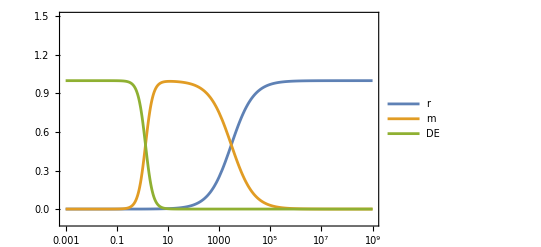

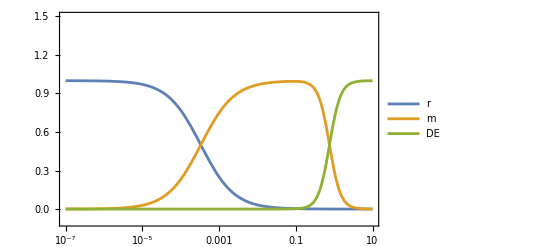

```mathematica
Plot[{(Ωr[1/z]),(Ωm[1/z]),(1-Ωm0-Ωr0)/h[1/z]^2},{z,10^-3,10^9},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^9},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
Plot[{(Ωr[a]),(Ωm[a]),(1-Ωm0-Ωr0)/h[a]^2},{a,10^-7,10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{0,10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

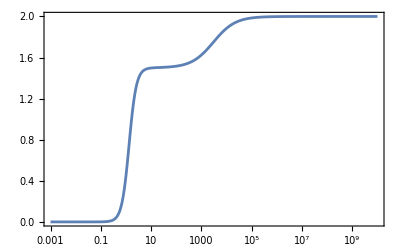

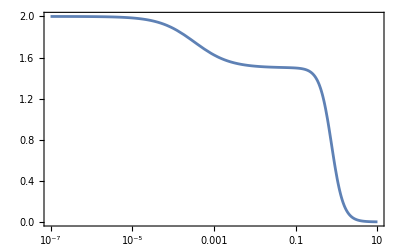

```mathematica
(*(Ḣ)/H^2=a/H dH/da y a=1/(z+1)*)
Plot[-h'[1/x]/h[1/x] 1/x,{x,10^-3,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{MaTeX["\\epsilon"]}]
Plot[-h'[a]/h[a]a,{a,10^-7,10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{MaTeX["\\epsilon"]}]
```

### Radiation epoch

```mathematica
h[a_]:=√(1-Ωr0-Ωm0+Ωr0 a^-4+Ωm0 a^-3)
Reduce[{a>=0,2-10^-2<=-D[h[a],a]/h[a]a<=2+10^-2},a]
ar=RandomPoint[ImplicitRegion[%,a]][[1]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤a≤6.80272×10^-6

5.14498×10^-6

```mathematica
Ωm[ar]
Ωr[ar]
(1-Ωr0-Ωm0)/h[ar]^2
%+%%+%%%
```

0.0152003

0.9848

4.82967×10^-18

1.

```mathematica
1-Ωr[ar]
```

0.000312551

```mathematica
(*Test favorable case for the radiation conditions*)
```

```mathematica
ϕ=0.7109046053664942
cg=2.17819628322409
C1=-2.610137764521424
C2=-0.18453102212567868

ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify);

NSolve[{(1-Ωr0-Ωm0)/h[ar]^2==(ΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[ar]+Ωm[ar])==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[Subscript[a, r]],y->ψ'[Subscript[a, r]],z->ψ''[Subscript[a, r]]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{(1-Ωr0-Ωm0)/h[ar]^2==(ΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[ar]+Ωm[ar])==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[Subscript[a, r]],y->ψ'[Subscript[a, r]],z->ψ''[Subscript[a, r]]}
```

0.710905

2.1782

-2.61014

-0.184531

{{ψ[a_r]→0.,ψ'[a_r]→101372.,ψ''[a_r]→5.11365×10^10},{ψ[a_r]→0.,ψ'[a_r]→-101372.,ψ''[a_r]→-5.11365×10^10},{ψ[a_r]→0.,ψ'[a_r]→170664.,ψ''[a_r]→-7.85695×10^8},{ψ[a_r]→0.,ψ'[a_r]→-170664.,ψ''[a_r]→7.85695×10^8}}

{{ψ[a_r]→0.,ψ'[a_r]→0.+5.00977×10^6 ⅈ,ψ''[a_r]→0.-5.74757×10^13 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.-5.00977×10^6 ⅈ,ψ''[a_r]→0.+5.74757×10^13 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.+227049. ⅈ,ψ''[a_r]→0.-9.98642×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.-227049. ⅈ,ψ''[a_r]→0.+9.98642×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-13086.+18500.9 ⅈ,ψ''[a_r]→7.20626×10^10-3.39198×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-13086.-18500.9 ⅈ,ψ''[a_r]→7.20626×10^10+3.39198×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→13086.+18500.9 ⅈ,ψ''[a_r]→-7.20626×10^10-3.39198×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→13086.-18500.9 ⅈ,ψ''[a_r]→-7.20626×10^10+3.39198×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→147664.+117418. ⅈ,ψ''[a_r]→-5.02372×10^10-1.1679×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→147664.-117418. ⅈ,ψ''[a_r]→-5.02372×10^10+1.1679×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-147664.+117418. ⅈ,ψ''[a_r]→5.02372×10^10-1.1679×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-147664.-117418. ⅈ,ψ''[a_r]→5.02372×10^10+1.1679×10^10 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-101368.,ψ''[a_r]→-5.11408×10^10},{ψ[a_r]→0.,ψ'[a_r]→101368.,ψ''[a_r]→5.11408×10^10},{ψ[a_r]→0.,ψ'[a_r]→170672.,ψ''[a_r]→-7.903×10^8},{ψ[a_r]→0.,ψ'[a_r]→-170672.,ψ''[a_r]→7.903×10^8}}

Exist some case viable with initial conditions on radiation?

```mathematica
ϕ=RandomReal[{0,√2}]
cg=RandomReal[{0,√((2-ϕ^2)/ϕ^4)}] 
C1=-2/(3 ϕ^4)
C2=(-2+ϕ^2+cg^2 ϕ^4)/(6 ϕ^4)

ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-2//Expand//Simplify);
NSolve[{(1-Ωr0-Ωm0)/h[ar]^2==(ΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[ar]+Ωm[ar])==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[a],y->ψ'[a],z->ψ''[a]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{(1-Ωr0-Ωm0)/h[ar]^2==(ΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[ar]+Ωm[ar])==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 ar,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[Subscript[a, r]],y->ψ'[Subscript[a, r]],z->ψ''[Subscript[a, r]]}
```

0.596693

3.52429

-5.25902

-0.0912967

{{ψ[a]→0.,ψ'[a]→218785.,ψ''[a]→4.2549×10^12},{ψ[a]→0.,ψ'[a]→-218785.,ψ''[a]→-4.2549×10^12},{ψ[a]→0.,ψ'[a]→1.22235×10^6,ψ''[a]→-1.56139×10^12},{ψ[a]→0.,ψ'[a]→-1.22235×10^6,ψ''[a]→1.56139×10^12}}

{{ψ[a_r]→0.,ψ'[a_r]→0.+2.75354×10^8 ⅈ,ψ''[a_r]→0.-1.34198×10^17 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.-2.75354×10^8 ⅈ,ψ''[a_r]→0.+1.34198×10^17 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.+1.55552×10^6 ⅈ,ψ''[a_r]→0.-4.49839×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→0.-1.55552×10^6 ⅈ,ψ''[a_r]→0.+4.49839×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→218780.,ψ''[a_r]→4.25509×10^12},{ψ[a_r]→0.,ψ'[a_r]→-218780.,ψ''[a_r]→-4.25509×10^12},{ψ[a_r]→0.,ψ'[a_r]→-46413.+102287. ⅈ,ψ''[a_r]→4.02763×10^12-9.66367×10^11 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-46413.-102287. ⅈ,ψ''[a_r]→4.02763×10^12+9.66367×10^11 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→46413.+102287. ⅈ,ψ''[a_r]→-4.02763×10^12-9.66367×10^11 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→46413.-102287. ⅈ,ψ''[a_r]→-4.02763×10^12+9.66367×10^11 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-1.07131×10^6+844068. ⅈ,ψ''[a_r]→2.90929×10^12-1.34164×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→-1.07131×10^6-844068. ⅈ,ψ''[a_r]→2.90929×10^12+1.34164×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→1.07131×10^6+844068. ⅈ,ψ''[a_r]→-2.90929×10^12-1.34164×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→1.07131×10^6-844068. ⅈ,ψ''[a_r]→-2.90929×10^12+1.34164×10^12 ⅈ},{ψ[a_r]→0.,ψ'[a_r]→1.2224×10^6,ψ''[a_r]→-1.56153×10^12},{ψ[a_r]→0.,ψ'[a_r]→-1.2224×10^6,ψ''[a_r]→1.56153×10^12}}

## Matter epoch try

```mathematica
h[a_]:=√(1-Ωr0-Ωm0+Ωr0 a^-4+Ωm0 a^-3)
Reduce[{a>=0,3/2-10^-2<=-D[h[a],a]/h[a]a<=3/2+10^-2},a]
am=RandomPoint[ImplicitRegion[%,a]][[1]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0163084≤a≤0.147489

0.137836

```mathematica
Ωm[am]
Ωr[am]
(1-Ωr0-Ωm0)/h[am]^2
%+%%+%%%
1-Ωm[am]
```

0.994075

0.00310446

0.00282014

1.

0.0059246

```mathematica
ϕ=RandomReal[{0,√2}]
cg=RandomReal[{0,√((2-ϕ^2)/ϕ^4)}] 
C1=-2/(3 ϕ^4)
C2=(-2+ϕ^2+cg^2 ϕ^4)/(6 ϕ^4)
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify);
NSolve[{(1-Ωr0-Ωm0)/h[am]^2==(ΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[am]+Ωm[am])==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[Subscript[a, m]],y->ψ'[Subscript[a, m]],z->ψ''[Subscript[a, m]]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{(1-Ωr0-Ωm0)/h[am]^2==(ΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[am]+Ωm[am])==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[Subscript[a, m]],y->ψ'[Subscript[a, m]],z->ψ''[Subscript[a, m]]}
```

0.0307719

1351.85

-743523.

-67003.1

{{ψ[a_m]→-0.0156385,ψ'[a_m]→-1.30598,ψ''[a_m]→139.041},{ψ[a_m]→0.0156385,ψ'[a_m]→1.30598,ψ''[a_m]→-139.041},{ψ[a_m]→0.0263349,ψ'[a_m]→0.110196,ψ''[a_m]→45.7103},{ψ[a_m]→-0.0263349,ψ'[a_m]→-0.110196,ψ''[a_m]→-45.7103}}

```mathematica
(*Test favorable case for today conditions*)
```

```mathematica
ϕ=0.7109046053664942
cg=2.17819628322409
C1=-2.610137764521424
C2=-0.18453102212567868
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify);


eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->-3/2//Expand//Simplify);

NSolve[{(1-Ωr0-Ωm0)/h[am]^2==(ΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[am]+Ωm[am])==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[Subscript[a, m]],y->ψ'[Subscript[a, m]],z->ψ''[Subscript[a, m]]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{(1-Ωr0-Ωm0)/h[ar]^2==(ΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[am]+Ωm[am])==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1 am,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[Subscript[a, m]],y->ψ'[Subscript[a, m]],z->ψ''[Subscript[a, m]]}
```

0.710905

2.1782

-2.61014

-0.184531

{{ψ[a_m]→-0.0349224,ψ'[a_m]→1.04941,ψ''[a_m]→-18.0907},{ψ[a_m]→0.0349224,ψ'[a_m]→-1.04941,ψ''[a_m]→18.0907},{ψ[a_m]→0.187902,ψ'[a_m]→-0.917267,ψ''[a_m]→14.3133},{ψ[a_m]→-0.187902,ψ'[a_m]→0.917267,ψ''[a_m]→-14.3133}}

{{ψ[a_m]→0.+1.19821 ⅈ,ψ'[a_m]→0.+187.555 ⅈ,ψ''[a_m]→0.-81310.2 ⅈ},{ψ[a_m]→0.-1.19821 ⅈ,ψ'[a_m]→0.-187.555 ⅈ,ψ''[a_m]→0.+81310.2 ⅈ},{ψ[a_m]→0.-0.345072 ⅈ,ψ'[a_m]→0.+7.50852 ⅈ,ψ''[a_m]→0.-131.233 ⅈ},{ψ[a_m]→0.+0.345072 ⅈ,ψ'[a_m]→0.-7.50852 ⅈ,ψ''[a_m]→0.+131.233 ⅈ},{ψ[a_m]→0.289388-0.482943 ⅈ,ψ'[a_m]→0.428537+0.84254 ⅈ,ψ''[a_m]→-95.9864-37.6292 ⅈ},{ψ[a_m]→0.289388+0.482943 ⅈ,ψ'[a_m]→0.428537-0.84254 ⅈ,ψ''[a_m]→-95.9864+37.6292 ⅈ},{ψ[a_m]→-0.289388-0.482943 ⅈ,ψ'[a_m]→-0.428537+0.84254 ⅈ,ψ''[a_m]→95.9864-37.6292 ⅈ},{ψ[a_m]→-0.289388+0.482943 ⅈ,ψ'[a_m]→-0.428537-0.84254 ⅈ,ψ''[a_m]→95.9864+37.6292 ⅈ},{ψ[a_m]→-0.373434+0.221356 ⅈ,ψ'[a_m]→4.95052+3.53289 ⅈ,ψ''[a_m]→-73.8452-25.9444 ⅈ},{ψ[a_m]→-0.373434-0.221356 ⅈ,ψ'[a_m]→4.95052-3.53289 ⅈ,ψ''[a_m]→-73.8452+25.9444 ⅈ},{ψ[a_m]→0.373434+0.221356 ⅈ,ψ'[a_m]→-4.95052+3.53289 ⅈ,ψ''[a_m]→73.8452-25.9444 ⅈ},{ψ[a_m]→0.373434-0.221356 ⅈ,ψ'[a_m]→-4.95052-3.53289 ⅈ,ψ''[a_m]→73.8452+25.9444 ⅈ},{ψ[a_m]→0.88565-0.0155832 ⅈ,ψ'[a_m]→4.89383+0.586279 ⅈ,ψ''[a_m]→37.9685-19.1391 ⅈ},{ψ[a_m]→0.88565+0.0155832 ⅈ,ψ'[a_m]→4.89383-0.586279 ⅈ,ψ''[a_m]→37.9685+19.1391 ⅈ},{ψ[a_m]→-0.88565-0.0155832 ⅈ,ψ'[a_m]→-4.89383+0.586279 ⅈ,ψ''[a_m]→-37.9685-19.1391 ⅈ},{ψ[a_m]→-0.88565+0.0155832 ⅈ,ψ'[a_m]→-4.89383-0.586279 ⅈ,ψ''[a_m]→-37.9685+19.1391 ⅈ}}

Today?

```mathematica
(*Test favorable case for today conditions*)
```

```mathematica
ϕ=0.7109046053664942
cg=2.17819628322409
C1=-2.610137764521424
C2=-0.18453102212567868
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->0//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->0//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}/.dh->0//Expand//Simplify);
NSolve[{(1-Ωr0-Ωm0)/h[1]^2==(ΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[1]+Ωm[1])==(PΩDE+ΩDE+4/3 Ωr0+Ωm0/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z},Reals]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
Ωm0=0.3;Ωr0=10^-4;ΩDE0=1-Ωm0-Ωr0;
NSolve[{(1-Ωr0-Ωm0)/h[1]^2==(ΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),(4/3 Ωr[1]+Ωm[1])==(PΩDE+ΩDE+1/3 Ωr0+Ωm0/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z}),0==(eomΩDE/.{a->1,ψ[a]->x,ψ'[a]->y,ψ''[a]->z})},{x,y,z}]/.{x->ψ[1],y->ψ'[1],z->ψ''[1]}
```

0.710905

2.1782

-2.61014

-0.184531

{{ψ[1]→1.35691,ψ'[1]→2.12918,ψ''[1]→-8.39747},{ψ[1]→-1.35691,ψ'[1]→-2.12918,ψ''[1]→8.39747},{ψ[1]→0.624728,ψ'[1]→0.551911,ψ''[1]→-2.55346},{ψ[1]→-0.624728,ψ'[1]→-0.551911,ψ''[1]→2.55346},{ψ[1]→-0.639964,ψ'[1]→0.0124298,ψ''[1]→0.117338},{ψ[1]→0.639964,ψ'[1]→-0.0124298,ψ''[1]→-0.117338}}

{{ψ[1]→0.+1.20071 ⅈ,ψ'[1]→0.+25.1464 ⅈ,ψ''[1]→0.-1495.01 ⅈ},{ψ[1]→0.-1.20071 ⅈ,ψ'[1]→0.-25.1464 ⅈ,ψ''[1]→0.+1495.01 ⅈ},{ψ[1]→-1.35691,ψ'[1]→-2.12918,ψ''[1]→8.3975},{ψ[1]→1.35691,ψ'[1]→2.12918,ψ''[1]→-8.3975},{ψ[1]→-0.0823223+0.280239 ⅈ,ψ'[1]→1.40219-0.376363 ⅈ,ψ''[1]→-5.44693+0.116007 ⅈ},{ψ[1]→-0.0823223-0.280239 ⅈ,ψ'[1]→1.40219+0.376363 ⅈ,ψ''[1]→-5.44693-0.116007 ⅈ},{ψ[1]→0.0823223+0.280239 ⅈ,ψ'[1]→-1.40219-0.376363 ⅈ,ψ''[1]→5.44693+0.116007 ⅈ},{ψ[1]→0.0823223-0.280239 ⅈ,ψ'[1]→-1.40219+0.376363 ⅈ,ψ''[1]→5.44693-0.116007 ⅈ},{ψ[1]→0.624716,ψ'[1]→0.551953,ψ''[1]→-2.55368},{ψ[1]→-0.624716,ψ'[1]→-0.551953,ψ''[1]→2.55368},{ψ[1]→0.+0.58568 ⅈ,ψ'[1]→0.-0.438612 ⅈ,ψ''[1]→0.-1.21494 ⅈ},{ψ[1]→0.-0.58568 ⅈ,ψ'[1]→0.+0.438612 ⅈ,ψ''[1]→0.+1.21494 ⅈ},{ψ[1]→0.639958,ψ'[1]→-0.0124945,ψ''[1]→-0.117094},{ψ[1]→-0.639958,ψ'[1]→0.0124945,ψ''[1]→0.117094},{ψ[1]→0.+3.22951 ⅈ,ψ'[1]→0.+2.71576 ⅈ,ψ''[1]→0.-0.113451 ⅈ},{ψ[1]→0.-3.22951 ⅈ,ψ'[1]→0.-2.71576 ⅈ,ψ''[1]→0.+0.113451 ⅈ}}

## Integration

```mathematica
Clear[h,C1,C2,cg]
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H'/H^2=1/H0 h'/h^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
ΩDE
PΩDE
eomΩDE
```

1/2 ((-6 C2+cg^2/h[a]^2) ψ[a]^4+2 a ψ[a] ψ'[a]+4 a (C1-4 C2) ψ[a]^3 ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1-6 a^2 C2 ψ'[a]^2))

1/6 ((4 C1 (3+dh)-2 C2 (3+2 dh)+cg^2/h[a]^2) ψ[a]^4+2 a ψ[a] ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1-6 a^2 (2 C1-3 C2) ψ'[a]^2)-4 a ψ[a]^3 ((C1 (1+dh)-C2 (4+dh)) ψ'[a]+a (C1-C2) ψ''[a]))

2 (C1 (3+dh)-2 C2 (3+2 dh)+cg^2/h[a]^2) ψ[a]^3+ψ[a] (2+dh-6 a^2 C2 ψ'[a]^2)+a ((4+dh) ψ'[a]+a ψ''[a])-6 a C2 ψ[a]^2 ((4+dh) ψ'[a]+a ψ''[a])

```mathematica
h[a_]:=√(1-Ωr0-Ωm0+Ωr0 a^-4+Ωm0 a^-3)
Reduce[{a>=0,2-10^-2<=-D[h[a],a]/h[a]a<=2+10^-2},a]
Reduce[{a>=0,3/2-10^-2<=-D[h[a],a]/h[a]a<=3/2+10^-2},a]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤a≤6.80272×10^-6

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0163084≤a≤0.147489

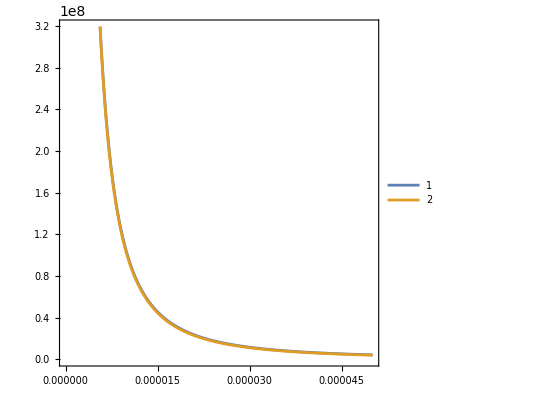

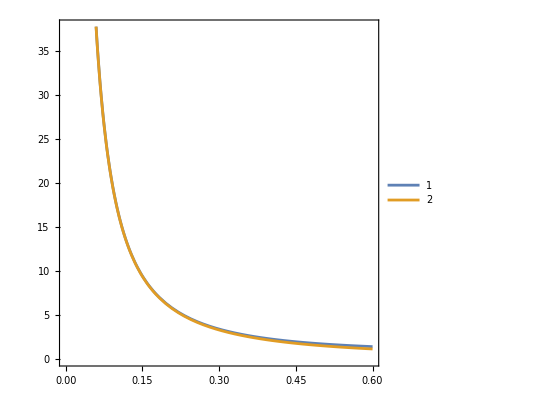

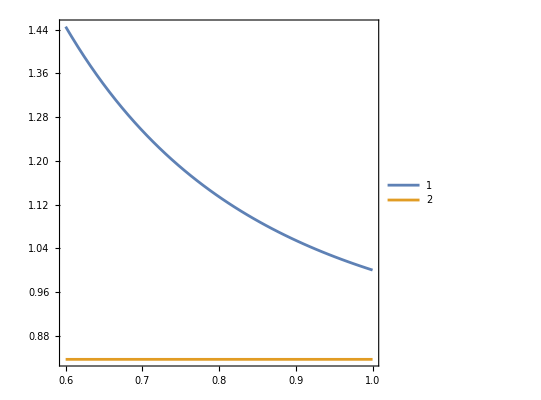

```mathematica
Plot[{h[a],√(Ωr0 a^-4)},{a,10^-10,5 10^-5},Frame->True,AspectRatio->1,PlotLegends->Automatic]
Plot[{h[a],√(Ωm0 a^-3)},{a,5 10^-5, 0.6},Frame->True,AspectRatio->1,PlotLegends->Automatic]
Plot[{h[a],√(1-Ωm0-Ωr0)},{a,0.6, 1},Frame->True,AspectRatio->1,PlotLegends->Automatic]
```

### Radiation

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωr0 a^-4);
dh=-2;
```

```mathematica
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solr=NDSolve[{eomΩDE==0,ψ[ar]==10^-8,ψ'[ar]==-1},ψ,{a,10^-10,5 10^-5}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[10^-6]/.Solr
```

0.0000213358

```mathematica
ΩDE/.a->10^-7/.Solr
```

1.32069×10^-11

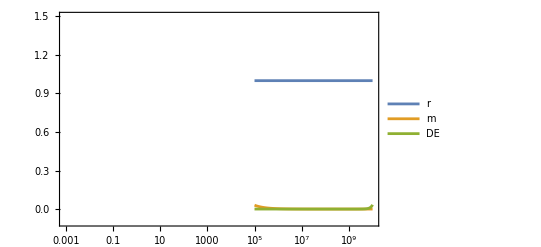

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωr0 (1/z)^-4)),((Ωm0(1/z)^-3)/(Ωr0 (1/z)^-4)),(ΩDE/.a->1/z/.Solr)},{z,10^5,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

### Matter

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωm0 a^-3);
dh=-3/2;
```

```mathematica
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solm=NDSolve[{eomΩDE==0,ψ[am]==2.7 10^-6,ψ'[am]==10^-4},ψ,{a,5 10^-5, 0.9}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solm
ψ'[0.6]/.Solm
```

8.84855×10^-6

-1.57456×10^-6

```mathematica
ΩDE/.a->0.5/.Solm
```

3.74631×10^-11

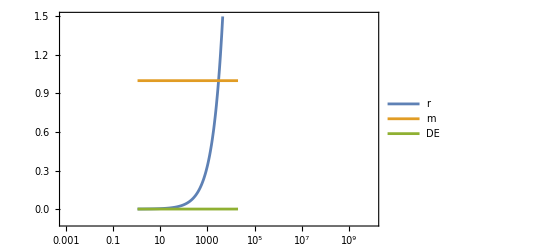

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωm0 (1/z)^-3)),((Ωm0(1/z)^-3)/(Ωm0 (1/z)^-3)),(ΩDE/.a->1/z/.Solm)},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

### Radiation and matter

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

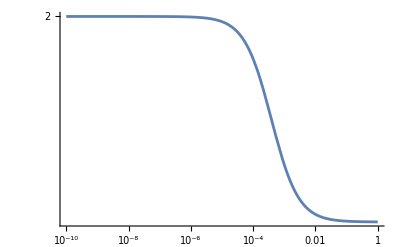

```mathematica
LogLogPlot[-dh,{a,10^-10,1},PlotRange->All]
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solrm=NDSolve[{eomΩDE==0,ψ[ar]==10^-6,ψ'[ar]==-1},ψ,{a,10^-10,0.7}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solrm
ψ'[0.6]/.Solrm
```

-1.92548×10^-7

1.55571×10^-7

```mathematica
ΩDE/.a->0.5/.Solrm
```

5.90675×10^-15

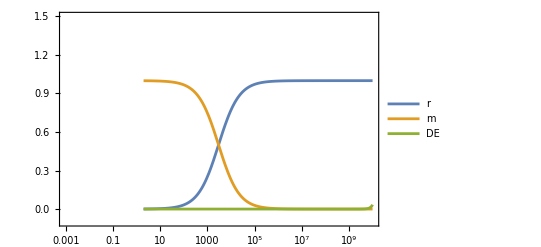

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωm0 (1/z)^-3+Ωr0 (1/z)^-4)),((Ωm0(1/z)^-3)/(Ωm0 (1/z)^-3+Ωr0 (1/z)^-4)),(ΩDE/.a->1/z/.Solrm)},{z,1/0.5,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

### The whole evolution assumin h as ΛCDM

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

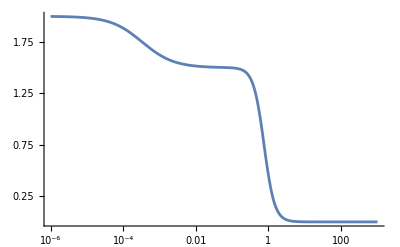

```mathematica
Plot[-dh,{a,10^-6,1000},PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solmr=NDSolve[{eomΩDE==0,ψ[am]==-10^-4,ψ'[am]==1.0520710081115596},ψ,{a,10^-10,100}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
Solrm=NDSolve[{eomΩDE==0,ψ[ar]==-10^-6,ψ'[ar]==1},ψ,{a,10^-10,100}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solrm
ψ'[0.6]/.Solrm
```

1.86598×10^-7

-1.75873×10^-7

```mathematica
ΩDE/.a->0.5/.Solrm
```

4.57618×10^-15

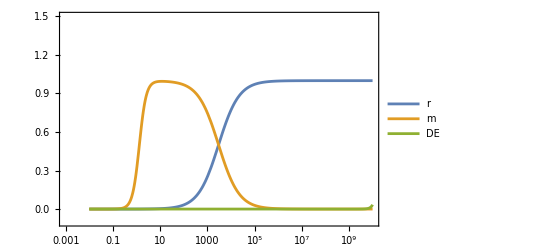

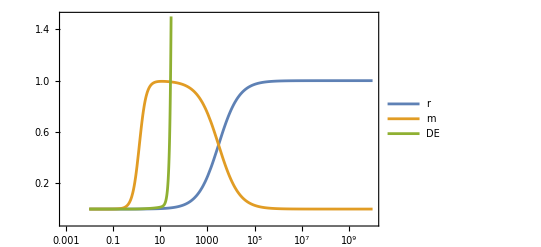

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2),((Ωm0(1/z)^-3)/h[1/z]^2),(ΩDE/.a->1/z/.Solrm)},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2),((Ωm0(1/z)^-3)/h[1/z]^2),(ΩDE/.a->1/z/.Solmr)},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

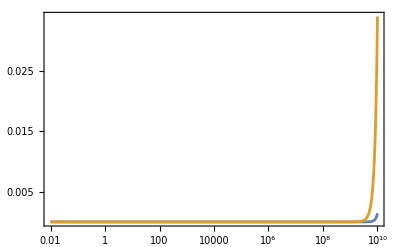

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

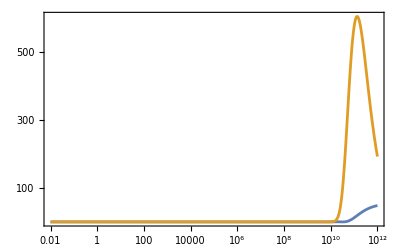

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(-6 ψ[a]^2(C2-C1)a 1/3 ψ[a]ψ'[a])/.a->1/z/.Solrm},{z,0.01,10^12},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

### DE epoch assuming ΛCDM, obvious not work!

```mathematica
Clear[h,dh,ϕ,cg,C1,C2,cc]
```

```mathematica
h[a_]=√(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
dh=0;
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
SolDE=NDSolve[{eomΩDE==0,ψ[10^8]==√1.8,ψ'[10^8]==-1},ψ,{a,0.7,10^10}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[2.4]/.SolDE
ψ'[2.4]/.SolDE
```

1.59296×10^15

-9.89761×10^14

```mathematica
ΩDE/.a->10^8/.SolDE
```

1.49647×10^16

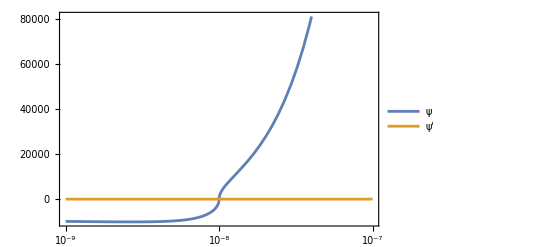

```mathematica
Plot[{ψ[1/z]/.SolDE,ψ'[1/z]/.SolDE},{z,10^-9,10^-7},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{"ψ","ψ'"}]
```

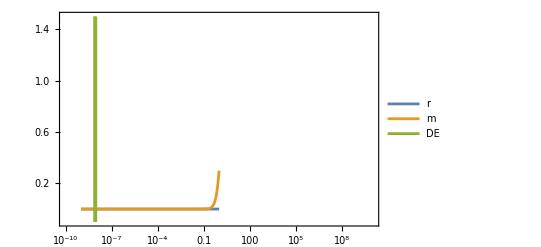

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2/.SolDE),((Ωm0(1/z)^-3)/h[1/z]^2/.SolDE),(ΩDE/.a->1/z/.SolDE)},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-10,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

### DE epoch

```mathematica
Clear[h,dh,ϕ,cg,C1,C2,cc]
```

```mathematica
ΩDE/.{ψ'[a]->0}
```

1/2 (ψ[a]^2+(-6 C2+cg^2/h[a]^2) ψ[a]^4)

```mathematica
h[a_]=1;
dh=0;
ϕ=0.7109046053664942;
cg=2.17819628322409;
C1=-2.610137764521424;
C2=-0.18453102212567868;
```

```mathematica
ΩDE/.{ψ'[a]->0}
Solve[(%)==1,ψ[a]]
```

1/2 (0.+1. ψ[a]^2+5.85173 ψ[a]^4)

{{ψ[a]→-0.710905},{ψ[a]→0.-0.822359 ⅈ},{ψ[a]→0.+0.822359 ⅈ},{ψ[a]→0.710905}}

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
SolDE=NDSolve[{eomΩDE==0,ψ[10^8]==-0.7109046053664941,ψ'[10^8]==10^-20},ψ,{a,0.7,10^10}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[2.4]/.SolDE
ψ'[2.4]/.SolDE
```

-6.31161×10^10

6.00353×10^10

```mathematica
ΩDE/.a->10^8/.SolDE
```

1.

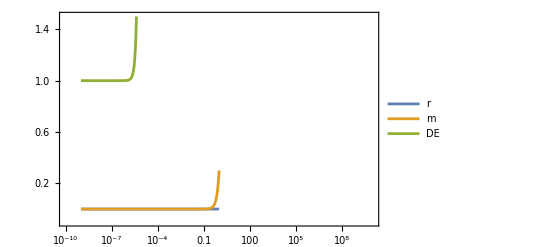

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2/.SolDE),((Ωm0(1/z)^-3)/h[1/z]^2/.SolDE),(ΩDE/.a->1/z/.SolDE)},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-10,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

```mathematica
ψ[10^8]/.SolDE
ϕ
```

-0.710905

0.710905

## Try in the case whe maybe there are not solutions.

```mathematica
Clear[h,dh,ϕ,cg,C1,C2,cc]
```

## Integration

```mathematica
Clear[h,C1,C2,cg]
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
ΩDE
PΩDE
eomΩDE
```

1/2 ((-6 C2+cg^2/h[a]^2) ψ[a]^4+2 a ψ[a] ψ'[a]+4 a (C1-4 C2) ψ[a]^3 ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1-6 a^2 C2 ψ'[a]^2))

1/6 ((4 C1 (3+dh)-2 C2 (3+2 dh)+cg^2/h[a]^2) ψ[a]^4+2 a ψ[a] ψ'[a]+a^2 ψ'[a]^2+ψ[a]^2 (1-6 a^2 (2 C1-3 C2) ψ'[a]^2)-4 a ψ[a]^3 ((C1 (1+dh)-C2 (4+dh)) ψ'[a]+a (C1-C2) ψ''[a]))

2 (C1 (3+dh)-2 C2 (3+2 dh)+cg^2/h[a]^2) ψ[a]^3+ψ[a] (2+dh-6 a^2 C2 ψ'[a]^2)+a ((4+dh) ψ'[a]+a ψ''[a])-6 a C2 ψ[a]^2 ((4+dh) ψ'[a]+a ψ''[a])

```mathematica
h[a_]:=√(1-Ωr0-Ωm0+Ωr0 a^-4+Ωm0 a^-3)
Reduce[{a>=0,2-10^-2<=-D[h[a],a]/h[a]a<=2+10^-2},a]
Reduce[{a>=0,3/2-10^-2<=-D[h[a],a]/h[a]a<=3/2+10^-2},a]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤a≤6.80272×10^-6

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0163084≤a≤0.147489

```mathematica
Plot[{h[a],√(Ωr0 a^-4)},{a,10^-10,5 10^-5},Frame->True,AspectRatio->1,PlotLegends->Automatic]
Plot[{h[a],√(Ωm0 a^-3)},{a,5 10^-5, 0.6},Frame->True,AspectRatio->1,PlotLegends->Automatic]
Plot[{h[a],√(1-Ωm0-Ωr0)},{a,0.6, 1},Frame->True,AspectRatio->1,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

### Radiation

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωr0 a^-4);
dh=-2;
```

```mathematica
cg=2;
C1=-3;
C2=-1;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solr=NDSolve[{eomΩDE==0,ψ[ar]==-10^-8,ψ'[ar]==10},ψ,{a,10^-10,5 10^-5}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[10^-6]/.Solr
```

-0.000339303

```mathematica
ΩDE/.a->10^-7/.Solr
```

3.02179×10^-9

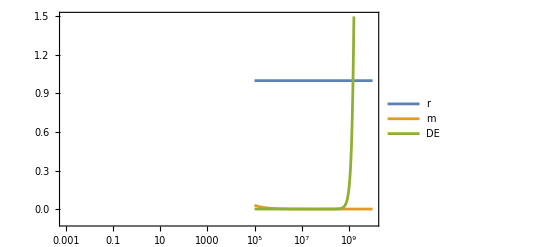

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωr0 (1/z)^-4)),((Ωm0(1/z)^-3)/(Ωr0 (1/z)^-4)),(ΩDE/.a->1/z/.Solr)},{z,10^5,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

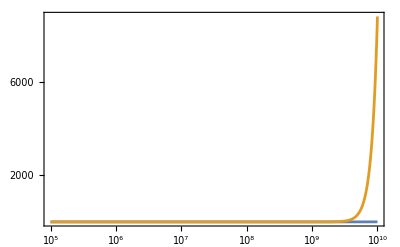

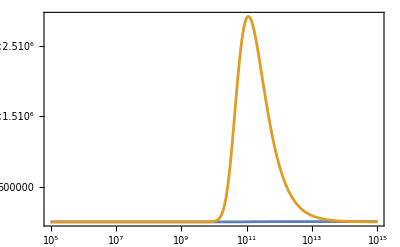

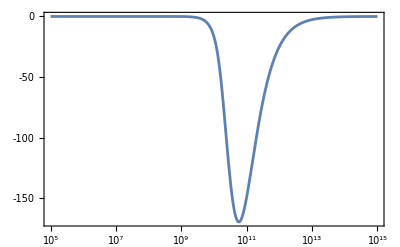

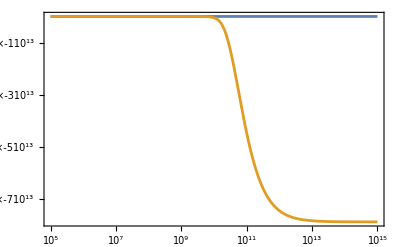

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solr,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solr},{z,10^5,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solr,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solr},{z,10^5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.Solr},{z,10^5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.Solr,ψ[a]ψ'[a]/.a->1/z/.Solr},{z,10^5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

### Matter

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωm0 a^-3);
dh=-3/2;
```

```mathematica
cg=2;
C1=-3;
C2=-1;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solm=NDSolve[{eomΩDE==0,ψ[am]==2.7 10^-6,ψ'[am]==10^-4},ψ,{a,5 10^-5, 0.9}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solm
ψ'[0.6]/.Solm
```

7.0042×10^-6

-2.26991×10^-6

```mathematica
ΩDE/.a->0.5/.Solm
```

1.91059×10^-11

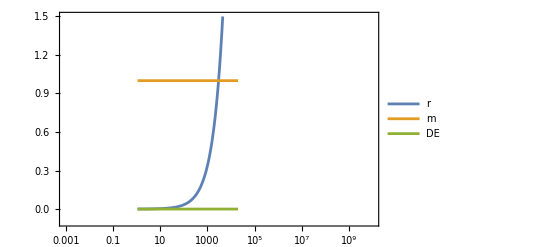

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωm0 (1/z)^-3)),((Ωm0(1/z)^-3)/(Ωm0 (1/z)^-3)),(ΩDE/.a->1/z/.Solm)},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

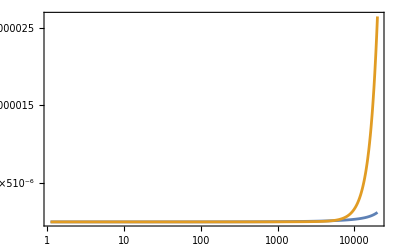

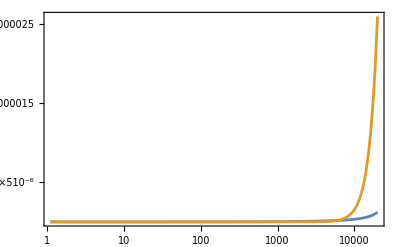

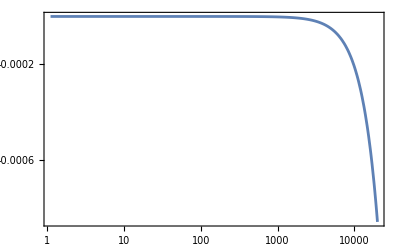

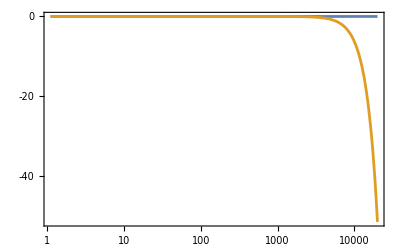

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solm,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solm},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solm,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solm},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.Solm},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.Solm,ψ[a]ψ'[a]/.a->1/z/.Solm},{z,1/0.9,1/5 10^5},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

### Radiation and matter

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
cg=2;
C1=-3;
C2=-1;
```

```mathematica
LogLogPlot[-dh,{a,10^-10,1},PlotRange->All]
```

-Graphics-

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solrm=NDSolve[{eomΩDE==0,ψ[ar]==10^-6,ψ'[ar]==-10},ψ,{a,10^-15,0.7}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solrm
ψ'[0.6]/.Solrm
```

-2.90302×10^-6

2.35859×10^-6

```mathematica
ΩDE/.a->0.5/.Solrm
```

1.32631×10^-12

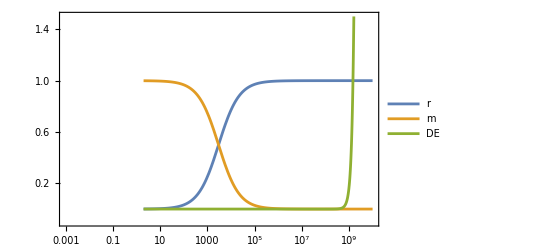

```mathematica
Plot[{((Ωr0(1/z)^-4)/(Ωm0 (1/z)^-3+Ωr0 (1/z)^-4)),((Ωm0(1/z)^-3)/(Ωm0 (1/z)^-3+Ωr0 (1/z)^-4)),(ΩDE/.a->1/z/.Solrm)},{z,1/0.5,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

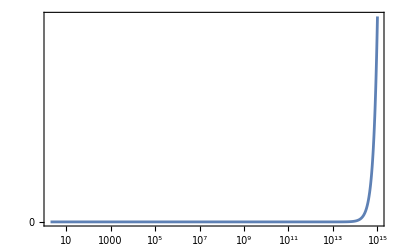

-Graphics-

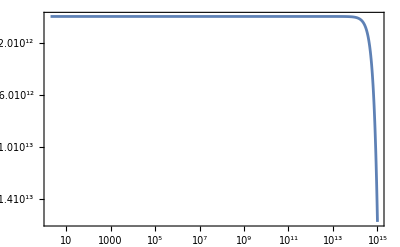

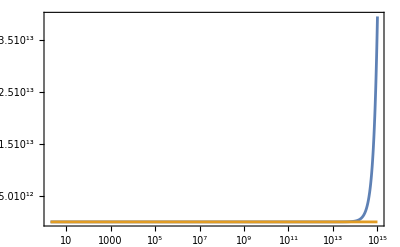

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.Solrm,ψ[a]ψ'[a]/.a->1/z/.Solm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

### The whole evolution assumin h as ΛCDM

```mathematica
Clear[h,dh,ϕ,cg,C1,C2]
```

```mathematica
h[a_]=√(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
cg=2;
C1=-3;
C2=-1;
```

```mathematica
Plot[-dh,{a,10^-6,1000},PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
Solmr=NDSolve[{eomΩDE==0,ψ[am]==-10^-4,ψ'[am]==1.0520710081115596},ψ,{a,10^-10,100}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
Solrm=NDSolve[{eomΩDE==0,ψ[ar]==-10^-6,ψ'[ar]==10^-10},ψ,{a,10^-10,100}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[0.6]/.Solrm
ψ'[0.6]/.Solrm
```

-4.5193×10^-8

4.26717×10^-8

```mathematica
ΩDE/.a->0.5/.Solrm
```

2.6956×10^-16

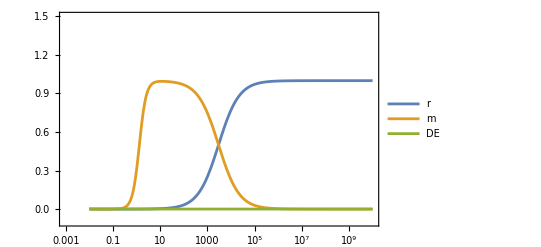

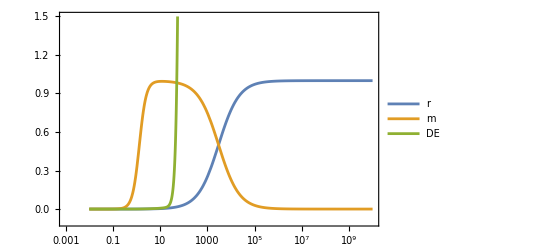

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2),((Ωm0(1/z)^-3)/h[1/z]^2),(ΩDE/.a->1/z/.Solrm)},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2),((Ωm0(1/z)^-3)/h[1/z]^2),(ΩDE/.a->1/z/.Solmr)},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-3,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

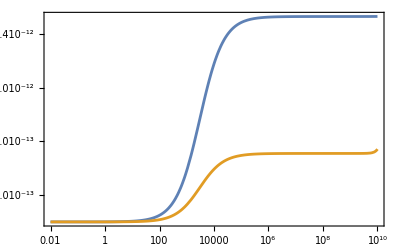

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,0.01,10^10},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

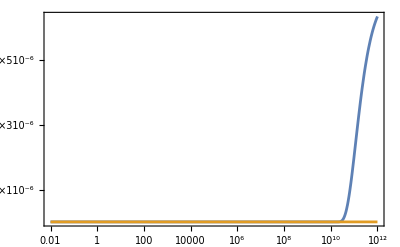

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(-6 ψ[a]^2(C2-C1)a 1/3 ψ[a]ψ'[a])/.a->1/z/.Solrm},{z,0.01,10^12},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

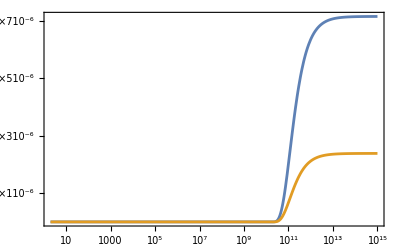

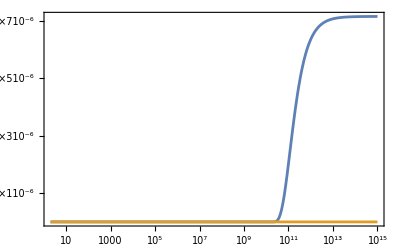

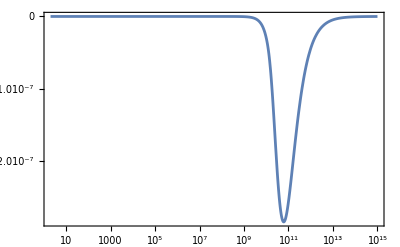

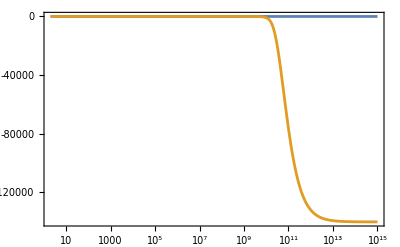

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.Solrm,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.Solrm,ψ[a]ψ'[a]/.a->1/z/.Solrm},{z,1/0.5,10^15},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

### DE epoch assuming ΛCDM, obvious not work!

```mathematica
Clear[h,dh,ϕ,cg,C1,C2,cc]
```

```mathematica
h[a_]=√(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4);
dh=-3/2((Ωm0 a^-3+4/3 Ωr0 a^-4)/(1-Ωm0-Ωr0+Ωm0 a^-3+Ωr0 a^-4));
```

```mathematica
cg=2;
C1=-3;
C2=-1;
```

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
SolDE=NDSolve[{eomΩDE==0,ψ[10^8]==√1.8,ψ'[10^8]==-1},ψ,{a,0.7,10^10}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[2.4]/.SolDE
ψ'[2.4]/.SolDE
```

2.54236×10^12

-1.15159×10^12

```mathematica
ΩDE/.a->10^8/.SolDE
```

5.9×10^16

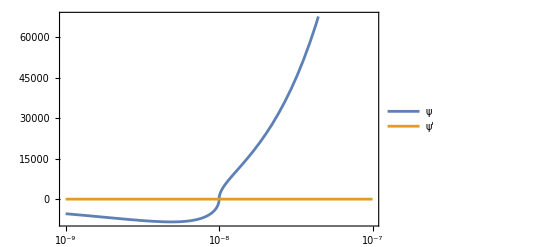

```mathematica
Plot[{ψ[1/z]/.SolDE,ψ'[1/z]/.SolDE},{z,10^-9,10^-7},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotLegends->{"ψ","ψ'"}]
```

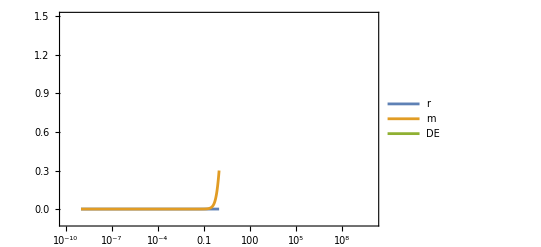

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2/.SolDE),((Ωm0(1/z)^-3)/h[1/z]^2/.SolDE),(ΩDE/.a->1/z/.SolDE)},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-10,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

```mathematica
Plot[{(ΩDE/.a->1/z/.SolDE)},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.SolDE,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.SolDE,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.SolDE,ψ[a]ψ'[a]/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### DE epoch

```mathematica
Clear[h,dh,ϕ,cg,C1,C2,cc]
```

```mathematica
ΩDE/.{ψ'[a]->0}
```

1/2 (ψ[a]^2+(-6 C2+cg^2/h[a]^2) ψ[a]^4)

```mathematica
h[a_]=1;
dh=0;
cg=2;
C1=-3;
C2=-1;
```

```mathematica
ΩDE/.{ψ'[a]->0}
Solve[(%)==1,ψ[a]]
```

ψ[a]^2/2+5 ψ[a]^4

{{ψ[a]→-√(2/5)},{ψ[a]→√(2/5)},{ψ[a]→-ⅈ/(√2)},{ψ[a]→ⅈ/(√2)}}

```mathematica
ΩDE=(rde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify (*dh=H0'/H0^2*));
PΩDE=(pde/(3 mP^2 H0[t[]]^2)/.RulesOfMotion/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);

eomΩDE=(eom2/mP/.{ψ''[a]->ψ''[a]mP,ψ'[a]->ψ'[a]mP,ψ[a]->ψ[a]mP,c1->C1/mP^2,c2->C2/mP^2,gh->cg/mP H0,H0[t[]]->H0 h[a],H0'[t[]]->H0^2 h[a]^2 dh}//Expand//Simplify);
```

```mathematica
SolDE=NDSolve[{eomΩDE==0,ψ[10^8]==√(2/5),ψ'[10^8]==-10^-20},ψ,{a,0.7,10^15}][[1]]
```

{ψ→InterpolatingFunction[…]}

```mathematica
ψ[2.4]/.SolDE
ψ'[2.4]/.SolDE
```

-1.03215×10^10

5.93125×10^9

```mathematica
ΩDE/.a->10^8/.SolDE
```

1.

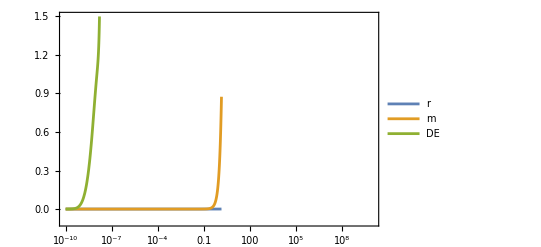

```mathematica
Plot[{((Ωr0(1/z)^-4)/h[1/z]^2/.SolDE),((Ωm0(1/z)^-3)/h[1/z]^2/.SolDE),(ΩDE/.a->1/z/.SolDE)},{z,10^-10,1/0.7},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{{10^-10,10^10},{-0.1,1.5}},PlotLegends->{"r","m","DE"}]
```

```mathematica
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.SolDE,(1/2(a ψ'[a]+ψ[a])^2+6 ψ[a]^2(-1/2 C2(a ψ'[a]+ψ[a])^2+cg^2/h[a]^2 ψ[a]^2-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{3/2(a ψ'[a]+ψ[a])^2/.a->1/z/.SolDE,(6 ψ[a]^2(-(C2-C1)a 1/3 ψ[a]ψ'[a]))/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{a 1/3 ψ[a]ψ'[a]/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
Plot[{ψ[1/z]^2/.SolDE,ψ[a]ψ'[a]/.a->1/z/.SolDE},{z,10^-9,1},Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},PlotRange->{All,All}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»